```mathematica
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"velocity tools","init.nb"}]];
```

### MultiMedia Ray Casting

#### segInt

```mathematica
segInt[{a_,b_},{c_,d_}]:=Block[{α,β},
(* intersect line segments *)
If[Chop[Det[{b-a,d-c}]]==0,
{},
{α,β}=LinearSolve[Transpose[{a-b,d-c}],d-b];
If[(0≤α≤1)&&(0≤β≤1),α a+(1-α)b,{}]
]
]
```

```mathematica
Manipulate[
Graphics[{
Line[pts⟦1;;2,;;⟧],Line[pts⟦3;;4,;;⟧],
PointSize[Large],Point[segInt[pts⟦1;;2,;;⟧,pts⟦3;;4,;;⟧]]
},ImageSize->Small,
PlotRange->{-{1,1},{1,1}}ᵀ,PlotLabel->AbsoluteTiming@segInt[pts⟦1;;2,;;⟧,pts⟦3;;4,;;⟧]]
,{{pts,{{0,0},{1,0.5},{1,1},{0.5,0}}},-{1,1},{1,1},Locator}
]
```

#### Brainstorm

Region Definitions

Ambient space and discrete polygonal (or implicit) media

Pros

Specifiable brdy vel

Each media has bdry hit

Cons

Bounded ambient space

How would overlapping boundaries work?

Region Functions

SegBdryHit

Returns dist to hit (compilable)

Returns hit point (not compilable)

Ray-Casting Pipeline

Maintain ActiveRayVect Bool vector and use Pick to index TrajList (Unstructured Array of Hit Points)

TrajInfo updated at each step, contains {hit point, refracted direction, time of previous hit, current medium index}

#### Implement

```mathematica
First@Timing@Quiet@defVel[F0,2{{0,1},{1,0},{0,-1},{-1,0}}]
First@Timing@Quiet@defVel[F1,{{-1,-1},{-1,1},{1,-1},{1,1},{2,0},{-1.5,0}}]
First@Timing@Quiet@defVel[F2,ℛ[π].#&/@{{-1,-1},{-1,1},{1,-1},{1,1},{2,0},{-1.5,0}}]
GraphicsRow[LabeledPolarHullPlot/@{F0,F1,F2}]
```

0.

0.

0.015625

-Graphics-

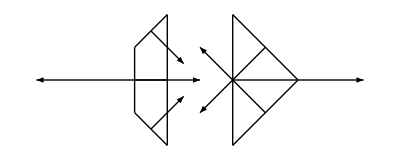

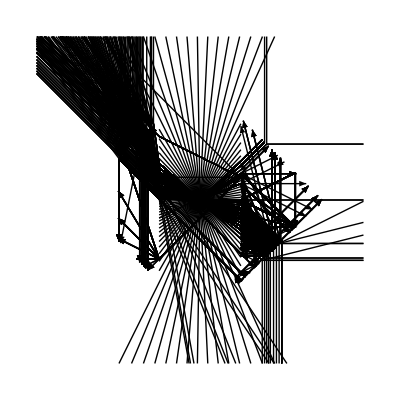

```mathematica
x0={0,0};T=5;

mCrd=4.;(* maximum x,y coordinate for trajectories *)
mDist=2 √2. mCrd;(* max dist *)
pw=Partition[mCrd{{-1,-1},{1,-1},{1,1},{-1,1}},2,1,1];

nRays=100;
(*activeRayVect=ConstantArray[True,nRays];*)
trajInfo=Table[{x0,mDist{Cos[θ],Sin[θ]},0,0,θ/(2π/(nRays-1))+1},{θ,0,2π,2π/(nRays-1)}];

FAmb=F2;
{F01,M1}={F0,{{-1,2},{-2,1},{-2,-1},{-1,-2}}};
{F02,M2}={F2,{{3,0},{1,2},{1,-2}}};
meds={{F01,M1},{F02,M2}};

m=Length@meds;
regBdry=Join[
AssociationThread[Range[m]->rotatedPairs/@meds⟦;;,2⟧],
<|Infinity->pw|>
];
regVel=Join[
AssociationThread[Range[m]->meds⟦;;,1⟧],
<|0->FAmb|>
];

bdryReg=Association@@KeyValueMap[Sequence@@Thread[#2->ConstantArray[#1,Length@#2]]&,regBdry];
bdryRegPair={0,#}&/@bdryReg;(* for now, everything borders ambient space *)

pb=Flatten[rotatedPairs/@meds⟦;;,2⟧,1];(* paired boundaries *)
walls=pb~Join~pw;

bdryNormals=AssociationThread[walls->(r90.(#⟦2⟧-#⟦1⟧)&/@walls)];

Graphics[{
KeyValueMap[{Line[#1],Arrow[{Mean@#1,Mean@#1+#2}]}&,bdryNormals[[;;-5]]]
}]

iStepVel[{pt_,dir_,T_,med_,_},{idx_}]:=If[NumberQ@med,
Block[{wall,n,medNew,F0=regVel[med],F1,ptHit,t,ζ,v2},
(* had to take first becasue it duplicates at veticies *)
{wall,ptHit}=First[MinimalBy[((pt-#).(pt-#)&)[Last@#]&]@DeleteCases[DeleteCases[{#,segInt[{pt,pt+dir},#]}&/@walls,{_,{}}],{_,pt}]];
medNew=SelectFirst[bdryRegPair[wall],#≠med&];
(*Echo[{wall,ptHit,medNew,idx}];*)
If[NumberQ@medNew,
n=bdryNormals[wall];
F1=regVel[medNew];
t=Subscript[γ, F0][ptHit-pt];
(*If[t==0,Echo[{ptHit,pt}]];*)
ζ=Subscript[𝒩̂, F0][(ptHit-pt)/t];
If[medNew==0,
v2=Select[discretize/@Subscript[RefractedVelocities, F1][ζ,-n],#.-n≥1&],
v2=Select[discretize/@Subscript[RefractedVelocities, F1][ζ,n],#.n≥1&]
];
If[SameQ[v2,{}],
{ptHit,Null,T+t,Infinity,idx},
Sequence@@({ptHit,mDist #,T+Subscript[γ, F0][ptHit-pt],medNew,idx}&/@v2)]
,
(* boundary medium hit *)
{ptHit,Null,T+Subscript[γ, F0][ptHit-pt],medNew,idx}
]
]
,
(* boundary medium previously hit *)
{pt,Null,T,med,idx}
]

results=NestList[MapIndexed[iStepVel,#]&,trajInfo,4];
(* complicated way of getting relevent data using indicies in above results *)
f[l1_,l2_]:=KeyValueMap[With[{first=l1⟦#1⟧},Sequence@@({If[Head@first⟦2⟧===List,Sequence@@(Most@first),first],#,Last@#}&/@#2)]&,GroupBy[Last]@l2]
paths=Fold[f,results⟦;;,;;,{1,3,-1}⟧];

Graphics[
Arrow/@paths⟦;;,;;-2⟧⟦;;,;;,1⟧
]
```

```mathematica
paths
```

{{{{0,0},0,1},{{1.,0.},0.666667,1},{{2.,-1.},1.66667,1},{{2.,-1.},1.66667,1},{{2.,-1.},1.66667,1},1},2873,{{{0,0},0,100},{{1.,0.},0.666667,100},{{2.,-1.},1.66667,156},{{2.,-1.},1.66667,485},{{2.,-1.},1.66667,950},950}}
 |  |  |  |

```mathematica
bdryNormals
```

<|{{-1,2},{-2,1}}→{1,-1},{{-2,1},{-2,-1}}→{2,0},{{-2,-1},{-1,-2}}→{1,1},{{-1,-2},{-1,2}}→{-4,0},{{3,0},{1,2}}→{-2,-2},{{1,2},{1,-2}}→{4,0},{{1,-2},{3,0}}→{-2,2},{{-4.,-4.},{4.,-4.}}→{0.,8.},{{4.,-4.},{4.,4.}}→{-8.,0.},{{4.,4.},{-4.,4.}}→{0.,-8.},{{-4.,4.},{-4.,-4.}}→{8.,0.}|>

```mathematica
paths
```

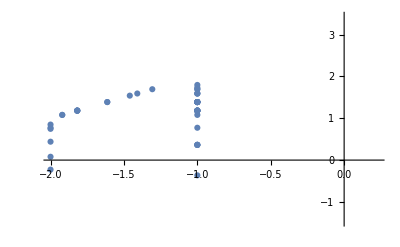

```mathematica
ListPlot@results[[-1,;;,1]]
```

```mathematica
{points,times}=paths[[-60,;;-2,{1,2}]]ᵀ
{points,times}=DeleteDuplicates/@{points,times}
pwParam[points_,times_]:=Block[{
vals=(((t-#2⟦2⟧)/(#2⟦1⟧-#2⟦2⟧))#1⟦1⟧+((t-#2⟦1⟧)/(#2⟦2⟧-#2⟦1⟧))#1⟦2⟧)&@@@({Most@rotatedPairs@points,Most@rotatedPairs@times}ᵀ),
cnds={t<#⟦1,2⟧,Sequence@@((#1≤t<#2&)@@@#⟦2;;-2⟧),#⟦-1,1⟧≤t}&@Most@rotatedPairs@times},
Function[{τ},Evaluate[Piecewise[{vals,cnds}ᵀ]/.t->τ]]
]
pwParam[points,times]
pwParam[points,times][1 Max@times]
Manipulate[
Graphics[{Table[{ColorData["NeonColors"][t/Max@times],Point[pwParam[points,times][t]]},{t,0,tm,0.01}],Black,PointSize[Large],Point/@points}]
,{{tm,Max@times},0,Max@times}]
```

{{{0,0},{1.,0.},{2.33333,-0.666667},{2.33333,-0.666667},{1.,0.666667}},{0,0.666667,1.77778,1.77778,3.11111}}

{{{0,0},{1.,0.},{2.33333,-0.666667},{2.33333,-0.666667},{1.,0.666667}},{0,0.666667,1.77778,1.77778,3.11111}}

Function[{τ},Piecewise[{{{0.+1.5 τ,0.}, τ<0.666667}, {{-0.9 (-1.77778+τ)+2.1 (-0.666667+τ),0.-0.6 (-0.666667+τ)}, 0.666667≤τ<1.77778}, {{-1.75 (-3.11111+τ)+0.75 (-1.77778+τ),0.5 (-3.11111+τ)+0.5 (-1.77778+τ)}, 1.77778≤τ}, {0, True}}]]

{1.,0.666667}

```mathematica
capsuleInterpolation[imgs_]:=With[{capsuleVects=capsnet[imgs,NetPort["Pick","Output"]]},Animate[Image[reconstructor[capsuleVects[[Floor[t+1]]]*(1-Mod[t,1])+capsuleVects[[Floor[t+2]]]*Mod[t,1]],ImageSize->200],{t,0,Length[imgs]-1.01,0.01}]]
```

```mathematica
trajInfo
```

{{{0,0},{28.2843,0.},0,0,1},{{0,0},{21.667,18.1808},0,0,2},{{0,0},{4.91151,27.8546},0,0,3},{{0,0},{-14.1421,24.4949},0,0,4},{{0,0},{-26.5785,9.67379},0,0,5},{{0,0},{-26.5785,-9.67379},0,0,6},{{0,0},{-14.1421,-24.4949},0,0,7},{{0,0},{4.91151,-27.8546},0,0,8},{{0,0},{21.667,-18.1808},0,0,9},{{0,0},{28.2843,0.},0,0,10}}

```mathematica
If[Head@First@first===List&&Head@Last@first===Number,Sequence@@first,first]
If[Head@first⟦2⟧===List,Sequence@@first,first]
```

```mathematica
Most@rotatedPairs@results;
```

```mathematica
bdryIdxs=AssociationThread[walls-> Range@Length@walls->(r90.(#⟦2⟧-#⟦1⟧)&/@)]
```

```mathematica
bdryReg
```

<|{{-1,-1},{0,-1}}→1,{{0,-1},{-1,0}}→1,{{-1,0},{-1,-1}}→1,{{1,0},{2,1}}→2,{{2,1},{2,2}}→2,{{2,2},{1,1}}→2,{{1,1},{1,0}}→2,{{-10.,-10.},{10.,-10.}}→∞,{{10.,-10.},{10.,10.}}→∞,{{10.,10.},{-10.,10.}}→∞,{{-10.,10.},{-10.,-10.}}→∞|>

```mathematica
arr={{a1,b1,c1},{{a1,b1,c1},{a1,b1,c1}},{a1,b1,c1}};
```

{a1,b1,c1,{a1,b1,c1},{a1,b1,c1},a1,b1,c1}

```mathematica
(* function idea: stepSim - takes old traj info, outputs new traj info*)
```

```mathematica
Timing[Table[RandomReal[]->RandomReal[],{10^6}];]
Timing[Table[{RandomReal[],RandomReal[]},{10^6}];]
```

{0.65625,Null}

{0.1875,Null}

#### Intersecting Faces

```mathematica
x0={0,0};

mCrd=10.;(* maximum x,y coordinate for trajectories *)
mDist=2 √2. mCrd;(* max dist *)
pw=Partition[mCrd{{-1,-1},{1,-1},{1,1},{-1,1}},2,1,1];

nRays=10;
activeRayVect=ConstantArray[True,nRays];
trajInfo=Table[{x0,mDist{Cos[θ],Sin[θ]},0,0},{θ,-π,π,2π/(nRays-1)}];

FAmb=F0;
{F01,M1}={F1,positivelyOrient@{{0,1},{1,0},{1,1}}};
{F02,M2}={F2,positivelyOrient@{{1,1},{1,0},{2,1},{2,2}}};
{F03,M3}={F1,positivelyOrient[-1{{0,1},{1,0},{1,1}}]};

M1~Join~M2
meds={{F01,M1},{F02,M2},{F03,M3}}
```

{{1,0},{1,1},{0,1},{1,0},{2,1},{2,2},{1,1}}

{{F1,{{1,0},{1,1},{0,1}}},{F2,{{1,0},{2,1},{2,2},{1,1}}},{F1,{{-1,-1},{0,-1},{-1,0}}}}

```mathematica
Outer[RegionIntersection,#,#]&[{M1,M2}]
```

{{Polygon[…],Line[{{1,0},{1,1}}]},{Line[{{1,0},{1,1}}],Polygon[…]}}

```mathematica
rotatedPairs/@{M1,M2,M3}
```

{{{{1,0},{1,1}},{{1,1},{0,1}},{{0,1},{1,0}}},{{{1,0},{2,1}},{{2,1},{2,2}},{{2,2},{1,1}},{{1,1},{1,0}}}}

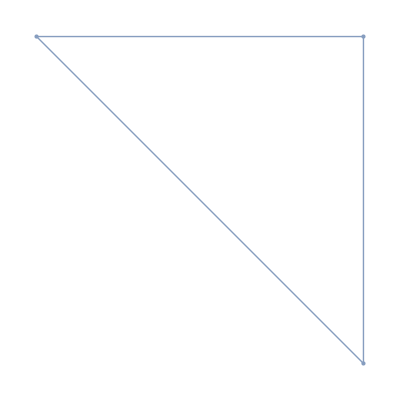
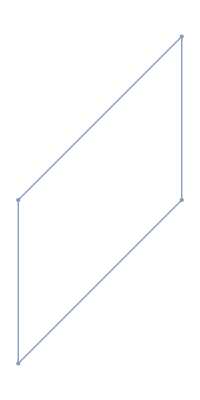
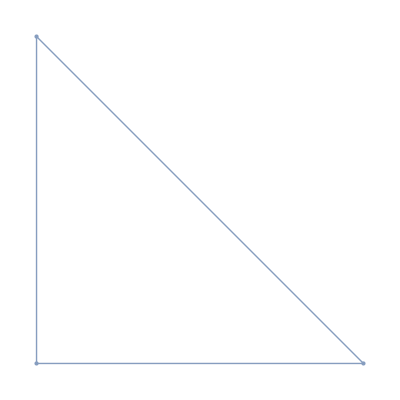

{{ConvexHullMesh[{{1,0},{1,1}}],ConvexHullMesh[{{1,1},{0,1}}],ConvexHullMesh[{{0,1},{1,0}}]},{ConvexHullMesh[{{1,0},{2,1}}],ConvexHullMesh[{{2,1},{2,2}}],ConvexHullMesh[{{2,2},{1,1}}],ConvexHullMesh[{{1,1},{1,0}}]},{ConvexHullMesh[{{-1,-1},{0,-1}}],ConvexHullMesh[{{0,-1},{-1,0}}],ConvexHullMesh[{{-1,0},{-1,-1}}]}}

{{{1,2},{1,3}},{{2,3}},{}}

{{1,2}→ImplicitRegion[x∈-Graphics-&&x∈-Graphics-,{x}],{1,3}→ImplicitRegion[x∈-Graphics-&&x∈-Graphics-,{x}],{2,3}→ImplicitRegion[x∈-Graphics-&&x∈-Graphics-,{x}]}

{{1,2}→ConvexHullMesh[{{1.,0.},{1.,1.}}]}

RegionDifference::reg: ConvexHullMesh[{{1,0},{1,1}}] is not a correctly specified region.

RegionDifference::reg: ConvexHullMesh[{{1,1},{0,1}}] is not a correctly specified region.

RegionDifference::reg: ConvexHullMesh[{{0,1},{1,0}}] is not a correctly specified region.

General::stop: Further output of RegionDifference::reg will be suppressed during this calculation.

{{RegionDifference[ConvexHullMesh[{{1,0},{1,1}}],ConvexHullMesh[{{1.,0.},{1.,1.}}]],RegionDifference[ConvexHullMesh[{{1,1},{0,1}}],ConvexHullMesh[{{1.,0.},{1.,1.}}]],RegionDifference[ConvexHullMesh[{{0,1},{1,0}}],ConvexHullMesh[{{1.,0.},{1.,1.}}]]}}

```mathematica
M=With[{l=Length@#},RegionBoundary@BoundaryMeshRegion[#,Line[Range[l]~Prepend~l]]]&/@meds⟦;;,2⟧
m=Length@M;
(*L=Line/@Flatten[rotatedPairs/@meds⟦;;,2⟧,1];*)
L=Map[ConvexHullMesh,rotatedPairs/@meds⟦;;,2⟧,{-3}]
(**)
Table[{i,j},{i,m},{j,i+1,m}]
Flatten[Table[{i,j}->ImplicitRegion[(x∈M⟦j⟧)∧(x∈M⟦i⟧),x],{i,m},{j,i+1,m}],1]
ints=Select[Flatten[
Table[
If[!SameQ[Head@#,MeshCoordinates],{i,j}->ConvexHullMesh@#,EmptyRegion[2]]&@MeshCoordinates@RegionIntersection[M⟦i⟧,M⟦j⟧]
,{i,m},{j,i+1,m}]
,1],SameQ[Head@#,Rule]&]
Table[With[{i1=int⟦1,1⟧,i2=int⟦1,2⟧,l=int⟦2⟧},
RegionDifference[#1,l]&/@L⟦i1⟧
],{int,ints}]
```

```mathematica
BoundaryMesh
```

```mathematica
ConvexHullMesh[{{1,0},{1,1},{1,.5}}]
```

ConvexHullMesh[{{1,0},{1,1},{1,0.5}}]

```mathematica
BoundaryMesh@ConvexHullMesh[{{1,0},{1,1}}]
```

BoundaryMesh[ConvexHullMesh[{{1,0},{1,1}}]]

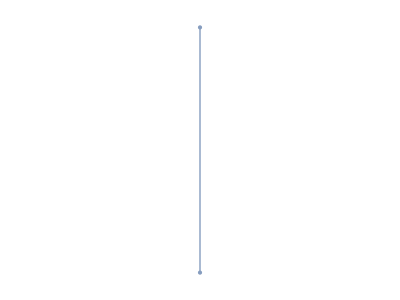
```mathematica
BoundaryMeshRegion[-Graphics-][[
```

```mathematica
BoundaryMeshRegion[-Graphics-]
```

{{-0.864271,-0.933004},{-0.99561,-0.578905},{0.496599,0.637906},{-0.601002,0.207916},{-0.693961,0.572511}}

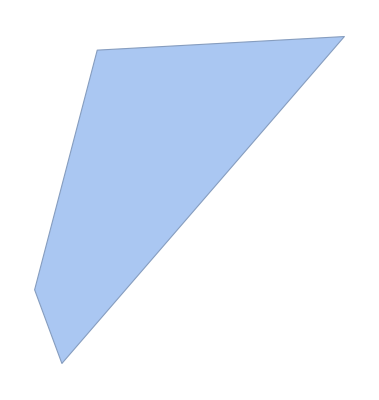

```mathematica
pts=RandomReal[{-1,1},{5,2}]
ConvexHullMesh[pts]
```

```mathematica
//FullForm//Last//Last
```

Last::normal: Nonatomic expression expected at position 1 in Last[].

Last[-Graphics-]

```mathematica
MeshCells[mr,1]
```

```mathematica
MeshRegion[{{1., 0.}, {1., 1.}}, {Line[{{1, 2}}]}][[1,1]]
```

Part::partd: Part specification ()⟦1,1⟧ is longer than depth of object.

(-Graphics-)⟦1,1⟧

```mathematica
RegionDifference[Line[{1,0},{1,1}],Line[{{1,0},{1,1}}]]
```

RegionDifference[Line[{1,0},{1,1}],Line[{{1,0},{1,1}}]]

Function::flpar: Parameter specification {i1,i2}→r in Function[{i1,i2}→r,r] should be a symbol or a list of symbols.

Function[{i1,i2}→r,r]

```mathematica
M
```

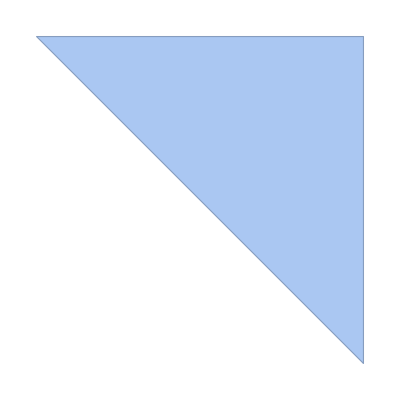
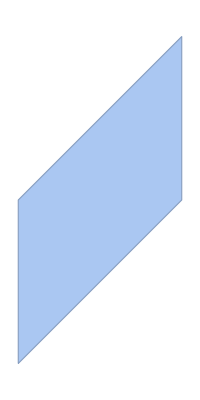
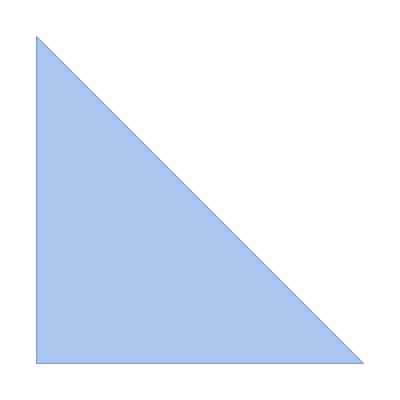
```mathematica
RegionIntersection[-Graphics-,-Graphics-]
RegionIntersection[-Graphics-,-Graphics-]
```

EmptyRegion[2]

EmptyRegion[2]

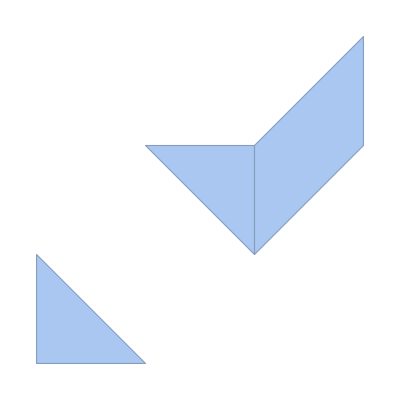

```mathematica
Show[M]
```

```mathematica
constMedium[F_,def_List/;(Length[def]≥3)]:=Block[{},
If[!SameQ[Head@F,Symbol],defVel[F]];
(* idea bdry hit *)
]
```

```mathematica
defMedia[FAmb_,med_]:=Module[{},
constMedium@@@med
]
```